```mathematica
f[e_,e0_,m_]:=HeavisideTheta[(e0-e)^2-m^2]Sqrt[(e0-e)^2-m^2]
```

```mathematica
ff[x_,m_,n_]:=Sum[f[x,10+2i/n,m],{i,0,n}]/n
```

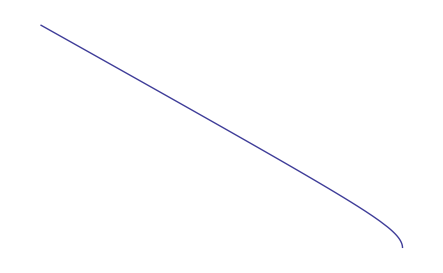

```mathematica
Plot[{f[x,10,1]},{x,0,9},Axes->False]
```